Importar los datos del sector simetrico:

```mathematica
(* Directorio con los datos *)
dir=FileNameJoin[{ParentDirectory@ParentDirectory@NotebookDirectory[],"DataBH"}];

(* Obtiene la lista de rutas completas de los archivos *)
archivos = FileNames["*Sym.csv", dir];

(* Importa cada archivo y los guarda en symData *)
symData = Import[#,"CSV"]&/@ archivos;
```

Vamos a quitar puntos para que no se vea muy bultoso, escogiendo datos equiespaciados en la escala log:

```mathematica
(* Obtiene y ordena la lista en un solo paso *)
archivos = SortBy[FileNames["*Sym.csv", dir], 
   ToExpression @ First @ StringCases[FileNameTake[#], DigitCharacter ..] &];

(* Importa los datos *)
symData = Import[#, "CSV"] & /@ archivos;
```

```mathematica
(* 1. Obtener el espaciamiento logarítmico de referencia (hasta 0.01) *)
xRef = symData[[1, All, 1]];
logXRef = Log10[Select[xRef, # <= 0.01 &]];
deltaLog = Median[Differences[logXRef]]; (* Usamos Mediana para mayor robustez *)

(* 2. Función para filtrar filas de una tabla *)
filtrarLog[tabla_] := Module[{lastLog = -Infinity},
  Select[tabla, If[Log10[#[[1]]] - lastLog >= deltaLog,
    lastLog = Log10[#[[1]]]; True, 
    False] &]
];

(* 3. Aplicar el filtro a todo tu symData *)
symDataFiltrado = Map[filtrarLog, symData];

n = Length[symDataFiltrado];
```

Gráfica:

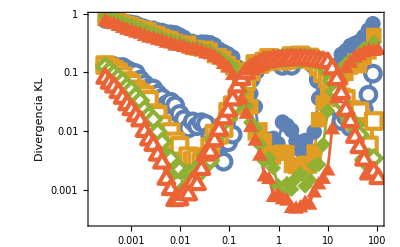

/home/jadeleon/Documents/practicas_Saul/InformeFinal/img/KL_Sym.pdf

```mathematica
(* Plot markers *)
formas = {
  Disk[], 
  Rectangle[{-1, -1}, {1, 1}], 
  Polygon[{{0, 1}, {1, 0}, {0, -1}, {-1, 0}}], (* Diamante *)
  Polygon[{{0, 1}, {-0.866, -0.5}, {0.866, -0.5}}], (* Triángulo *)
};

opacidadVal=1.;
(* Font size scaling, entre 0 y 1*)
fsScaling=0.02;
markerSize=16;

fig=ListLogLogPlot[
  Flatten[Table[{d[[All, {1, 3}]], d[[All, {1, 4}]]}, {d, symDataFiltrado}], 1],
  PlotRange -> All,
  Frame -> True,
  Joined -> True,
  LabelStyle -> Directive[Black,FontSize->Scaled[fsScaling]],
  ImageSize -> Full,
  PlotStyle -> Flatten[Table[{ColorData[97, i], ColorData[97, i]}, {i, n}]],
  PlotMarkers -> Flatten[Table[
    With[{shape = formas[[Mod[i - 1, Length[formas]] + 1]], col = ColorData[97, i]},
      {
        {Graphics[{Directive[col, Opacity[opacidadVal]], shape}], markerSize},
        {Graphics[{EdgeForm[{Directive[col, Opacity[opacidadVal]], Thickness[0.15]}], 
                   FaceForm[White], shape}], markerSize}
      }
    ], {i, n}], 1],
  FrameLabel -> {None, "Divergencia KL"},
  (* Agregamos la leyenda con 1 línea por color *)
  PlotLegends -> Placed[LineLegend[
    Table[Directive[ColorData[97,i],AbsoluteThickness[4]],{i,n}], {"TemplateBox[<|\"boxes\" -> FormBox[RowBox[{StyleBox[\"N\", \"TI\"], \"==\", StyleBox[\"L\", \"TI\"], \"==\", \"7\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"N=L=7\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]", "TemplateBox[<|\"boxes\" -> FormBox[RowBox[{StyleBox[\"N\", \"TI\"], \"==\", StyleBox[\"L\", \"TI\"], \"==\", \"8\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"N=L=8\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]", "TemplateBox[<|\"boxes\" -> FormBox[RowBox[{StyleBox[\"N\", \"TI\"], \"==\", StyleBox[\"L\", \"TI\"], \"==\", \"9\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"N=L=9\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]", "TemplateBox[<|\"boxes\" -> FormBox[RowBox[{StyleBox[\"N\", \"TI\"], \"==\", StyleBox[\"L\", \"TI\"], \"==\", \"10\"}], TraditionalForm], \"errors\" -> {}, \"input\" -> \"N=L=10\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]"},
    LegendMarkers -> None, (* <--- Esto quita los símbolos y deja solo la línea *)
    LegendMarkerSize -> {30,10}, (* Opcional: hace que el segmento de línea sea más largo *)
    LabelStyle -> {Black, FontSize->Scaled[fsScaling]},
Spacings->{0.1,0.3}
  ], {Left, Bottom}],
 GridLines->Automatic,
 GridLinesStyle->Directive[Gray,Dashed,Thickness[0.002],Opacity[0.75]],
 FrameStyle->Directive[Thickness[0.0025]],
FrameTicksStyle->{Directive[FontOpacity->0],Automatic,Directive[FontOpacity->0],Automatic}
]

Export[FileNameJoin[{NotebookDirectory[],"KL_Sym.pdf"}],fig]
```